```mathematica
Style[Text[":0421 :043f:043e:043c:043e:0449:044c:044e :043c:0435:0442:043e:0434:0430 :0441:0435:0442:043e:043a :0440:0435:0448:0438:0442:044c :0441:043b:0435:0434:0443:044e:0449:0438:0435 :0437:0430:0434:0430:0447:0438 :041a:043e:0448:0438 :0434:043b:044f :0443:0440:0430:0432:043d:0435:043d:0438:0439 :0441 :0447:0430:0441:0442:043d:044b:043c:0438 :043f:0440:043e:0438:0437:0432:043e:0434:043d:044b:043c:0438 :0441 :0442:043e:0447:043d:043e:0441:0442:044c:044e 10  :0441 :0448:0430:0433:043e:043c h=h=0.05 :043f:043e TraditionalForm`x\ :043d:0430 :043e:0442:0440:0435:0437:043a:0435 [0, 2], TraditionalForm`t∈[0, 3]. :041f:043e:0441:043b:0435 :043f:043e:043b:0443:0447:0435:043d:0438:044f :0437:043d:0430:0447:0435:043d:0438:0439 :0432 :0443:0437:043b:0430:0445 :0441:0435:0442:043a:0438, :043f:043e:0441:0442:0440:043e:0438:0442:044c :043f:043e :043d:0438:043c :0438:043d:0442:0435:0440:043f:043e:043b:044f:0446:0438:043e:043d:043d:0443:044e :0444:0443:043d:043a:0446:0438:044e Interpolation, :0430 :043f:043e:0442:043e:043c TraditionalForm` -  :0435:0451 :0433:0440:0430:0444:0438:043a. "],FontSize->20]
Style[Text["TraditionalForm`6"],FontSize->16]
```

С помощью метода сеток решить следующие задачи Коши для уравнений с частными производными с точностью 10  с шагом h=h=0.05 по TraditionalForm`x\ на отрезке [0, 2], TraditionalForm`t∈[0, 3]. После получения значений в узлах сетки, построить по ним интерполяционную функцию Interpolation\!\(\*StyleBox[",",FontFamily->"Times New Roman"]\)\!\(\*StyleBox[" ",FontFamily->"Times New Roman"]\)\!\(\*StyleBox["а",FontFamily->"Times New Roman"]\)\!\(\*StyleBox[" ",FontFamily->"Times New Roman"]\)\!\(\*StyleBox["потом",FontFamily->"Times New Roman"]\) \!\(\(TraditionalForm\` - \)\) \!\(\*StyleBox["её",FontFamily->"Times New Roman"]\)\!\(\*StyleBox[" ",FontFamily->"Times New Roman"]\)\!\(\*StyleBox["график",FontFamily->"Times New Roman"]\)\!\(\*StyleBox[".",FontFamily->"Times New Roman"]\)

TraditionalForm`6

x[i]:

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.}

t[i]:

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.}

Значения на границах сетки:

u(x,0):

{0,1.00428,2.00855,3.01283,4.01711,5.02138,6.02566,7.02994,8.03421,9.03849,10.0428,11.047,12.0513,13.0556,14.0599,15.0642,16.0684,17.0727,18.077,19.0813,20.0855,21.0898,22.0941,23.0984,24.1026,25.1069,26.1112,27.1155,28.1198,29.124,30.1283,31.1326,32.1369,33.1411,34.1454,35.1497,36.154,37.1582,38.1625,39.1668,1}

u(0,t):

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.}

u(2,t):

{1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.}

{{{0.,0.,0.},{0.,0.05,0.05},{0.,0.1,0.1},{0.,0.15,0.15},{0.,0.2,0.2},{0.,0.25,0.25},49,{0.,2.75,2.75},{0.,2.8,2.8},{0.,2.85,2.85},{0.,2.9,2.9},{0.,2.95,2.95},{0.,3.,3.}},39,{1}}
 |  |  |  |

InterpolatingFunction[…]

-Graphics-

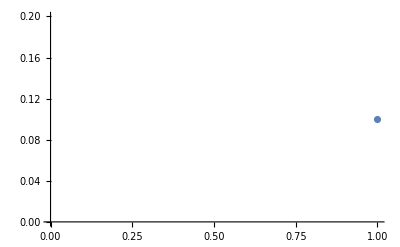

{0.1,p_(1,2),p_(2,2),p_(3,2),p_(4,2),p_(5,2),p_(6,2),p_(7,2),p_(8,2),p_(9,2),p_(10,2),p_(11,2),p_(12,2),p_(13,2),p_(14,2),p_(15,2),p_(16,2),p_(17,2),p_(18,2),p_(19,2),p_(20,2),p_(21,2),p_(22,2),p_(23,2),p_(24,2),p_(25,2),p_(26,2),p_(27,2),p_(28,2),p_(29,2),p_(30,2),p_(31,2),p_(32,2),p_(33,2),p_(34,2),p_(35,2),p_(36,2),p_(37,2),p_(38,2),p_(39,2),p_(40,2)}

```mathematica
Clear["Global`*"]
u[x_,t_]:=t/;x==0;
u[x_,t_]:=1+t/;x==2;
u[x_,t_]:=E^3*x/;t==0;
f[x_,t_]:=x*E^t;
eps=10^-9;
system=u[x,t]==(u[x+s,t]+u[x-s,t]+u[x,t+s]+u[x,t-s])/4;
h=0.05;
l=0.05;
a1=0;
b1=2;
a2=0;
b2=3;
m=(b1-a1)/h;
n=(b2-a2)/l;
(*solMatrix=Table[]*)
(*Solve[u[x,t]==(u[x+h,t]+u[x-h,t]+u[x,t+l]+u[x,t-l])/4]
DSolve[D[u[x,t],t]==16*D[D[u[x,t],x],x]+x*E^t,u,{x,t}]*)
Clear[x,t]
Print["x[i]:"];
For[i=0,i<=m,i++,
x[i]=i*h;
]
Table[x[i],{i,0,m}]
Print["t[i]: "];
For[i=0,i≤n,i++,
t[i]=i*l;
]
Table[t[i],{i,0,n}]
Print["Значения на границах сетки: "];
Print["u(x,0):"];
Table[Subscript[p, i,0]=u[x[i],0],{i,0,m}]
Print["u(0,t):"];
Table[Subscript[p, 0,i]=u[0,t[i]],{i,0,n}]
Print["u(2,t):"];
Table[Subscript[p, n,i]=u[2,t[i]],{i,0,n}]
Do[
Subscript[p, i,k+1]=Subscript[p, i,k]+81*(Subscript[p, i-1,j]+Subscript[p, i+1,j]-2*Subscript[p, i,j])+ h*f[x[i],t[k]],{j,0,n-1},{i,1,m-1}
]
(*For[i=1,i≤m-1,i++,
For[j=0,j≤n-1,j++,
Subscript[y, i,j+1]=Subscript[y, i,j]+81*(Subscript[y, i-1,j]+Subscript[y, i+1,j]-2 Subscript[y, i,j])+ h*f[x[i],t[k]]
];
];*)
Table[{x[i],t[j],Subscript[p, i,j]},{i,0,m},{j,0,n}]
points[j_]:=Table[Subscript[p, i,j],{i,0,m}];
Interpolation[points[2]]
Plot[Interpolation[points[2]][x],{x,1,5}]
ListPlot[points[2]]
points[2]
```